```mathematica
SetDirectory[NotebookDirectory[]]

getregion[id_]:=If[id==186,Green,
If[id<75,Gray,
If[id>=75 && id<150,Red,
If[id>=150 && id<250 && id!=186,Blue,
If[id>=250,Purple,White]]]]]
```

/Users/masauer2/IBMDataPreProcess/pythonProject/scripts/09_model_eval

```mathematica
data = Import["../09_model_eval/output/feature_importances.txt","Table"];
```

```mathematica
colnames = data[[1]];
meanfeatureimp = Mean[data[[2;;]]];
stdfeatureimp = StandardDeviation[data[[2;;]]];
```

```mathematica
keeper = Table[
If[meanfeatureimp[[i]]>0,i,##&[]]
,{i,1,Length[meanfeatureimp]}]
```

{7,12,16,20,31,43,44,47,48,50,71,85,93,102,115,119,149,151,175,176,182,191,193}

```mathematica
meankeeperorder =Ordering[meanfeatureimp[[keeper]]];
meankeeper = meanfeatureimp[[keeper]];
stdkeeper =stdfeatureimp[[keeper]];
colkeeper = colnames[[keeper]];
meankeeper = Table[meankeeper[[meankeeperorder[[i]]]],{i,1,Length[meankeeper]}]
stdkeeper = Table[stdkeeper[[meankeeperorder[[i]]]],{i,1,Length[stdkeeper]}]
colkeeper = Table[colkeeper[[meankeeperorder[[i]]]],{i,1,Length[colkeeper]}]
```

{1.29353×10^-6,2.87451×10^-6,3.01824×10^-6,6.89883×10^-6,0.0000549032,0.0000948589,0.000159104,0.000160829,0.000760165,0.000882763,0.00130374,0.00160254,0.00175446,0.00192204,0.00228366,0.00259367,0.00381764,0.00625307,0.00641634,0.00962631,0.012012,0.0288881,0.0401087}

{4.13389×10^-6,5.77799×10^-6,5.88356×10^-6,7.21671×10^-6,0.000129931,0.0000752249,0.0000606088,0.0000720714,0.000188947,0.0000985477,0.000101286,0.000280363,0.000246922,0.000123922,0.000127736,0.000154317,0.00018717,0.000222952,0.000214878,0.000292373,0.000309521,0.000491339,0.000606329}

{111_101,131_98,129_229,319_84,324_123,126_100,127_226,286_172,132_229,195_222,315_120,193_225,111_99,318_117,104_98,191_226,108_64,322_80,56_174,106_93,106_222,186_356,187_357}

```mathematica
plotme = Table[Around[meankeeper[[i]],stdkeeper[[i]]],{i,1,Length[meankeeper]}]
colors=getregion[ToExpression[StringSplit[#,"_"][[1]]]]&/@colkeeper
```

{1.4.10^-6,3.6.10^-6,3.6.10^-6,7.7.10^-6,0.000050.00013,0.000090.00008,0.000160.00006,0.000160.00007,0.000760.00019,0.000880.00010,0.001300.00010,0.001600.00028,0.001750.00025,0.001920.00012,0.002280.00013,0.002590.00015,0.003820.00019,0.006250.00022,0.006420.00021,0.009630.00029,0.012010.00031,0.02890.0005,0.04010.0006}

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],GrayLevel[0.5],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

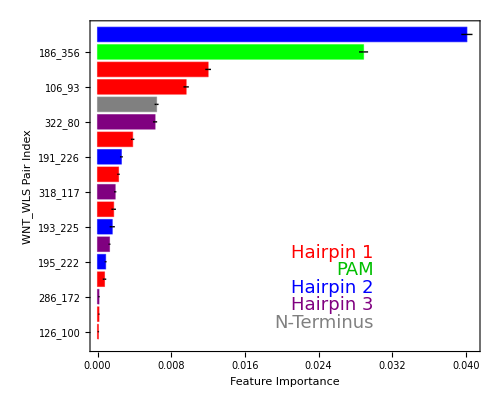

feature_importance.jpg

```mathematica
plt = Show[BarChart[plotme[[6;;]],ChartLabels->colkeeper[[6;;]],BarOrigin->Left,ChartStyle->colors[[6;;]],BaseStyle->{FontSize->12},Frame->True,FrameLabel->{{Style["WNT_WLS Pair Index",FontSize->18],None},{Style["Feature Importance",FontSize->18],None}},FrameStyle->Directive[Black,Thickness[0.003]]],
Graphics[Text[Style["Hairpin 1",FontColor->Red,FontSize->18],{0.03,5.5},Right]],
Graphics[Text[Style["PAM",FontColor->RGBColor[0,0.75,0],FontSize->18],{0.03,4.5},Right]],
Graphics[Text[Style["Hairpin 2",FontColor->Blue,FontSize->18],{0.03,3.5},Right]],
Graphics[Text[Style["Hairpin 3",FontColor->Purple,FontSize->18],{0.03,2.5},Right]],
Graphics[Text[Style["N-Terminus",FontColor->Gray,FontSize->18],{0.03,1.5},Right]],
ImageSize->500,AspectRatio->1/1.2]
Export["feature_importance.jpg",Magnify[plt,8.0]]
```